## 852 qwp:

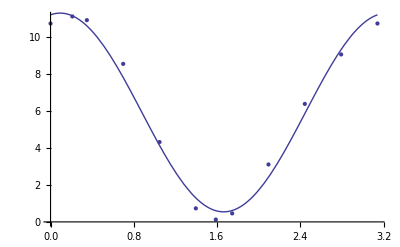

```mathematica
bkgrd=9.9 10^-3;
angles= Join[Table[i,{i,0,180,20}],{192-180,271-180}]π/180;
powers={10.72,10.9,8.54,4.32,0.741,.469,3.11,6.38,9.05,10.72,11.1,0.136}-bkgrd;
data=Thread[{angles,powers}];
fitfn=A Cos[ 2(θ+θ0)] + Offs;
fit=FindFit[data,fitfn, {θ0,{A,5},{Offs,5}},θ];
Show[
{ListPlot[data],
Plot[fitfn/.fit,{θ,0,π}]
}
]
```

## dual qwp-852:

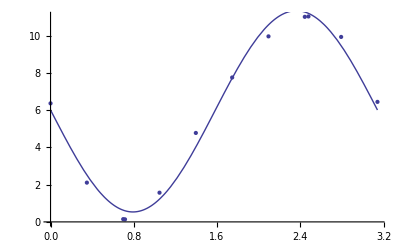

```mathematica
bkgrd=9.9 10^-3;
angles= Join[Table[i,{i,0,180,20}],{322-180,41}]π/180;
powers={6.38,2.12,0.157,1.58,4.79,7.77,9.98,11.03,9.95,6.46,11.05,0.147}-bkgrd;
data=Thread[{angles,powers}];
fitfn=A Cos[ 2(θ+θ0)] + Offs;
fit=FindFit[data,fitfn, {θ0,{A,5},{Offs,5}},θ];
Show[
{ListPlot[data],
Plot[fitfn/.fit,{θ,0,π}]
}
]
```

## 589 qwp:

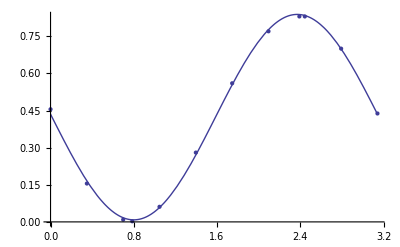

```mathematica
bkgrd=0;
angles= Join[Table[i,{i,0,180,20}],{137,45}]π/180;
powers={0.455,0.155,0.0092,0.061,0.28,0.56,0.77,0.83,0.70,0.438,0.83,0.00245}-bkgrd;
data=Thread[{angles,powers}];
fitfn=A Cos[ 2(θ+θ0)] + Offs;
fit=FindFit[data,fitfn, {θ0,{A,5},{Offs,5}},θ];
Show[
{ListPlot[data],
Plot[fitfn/.fit,{θ,0,π}]
}
]
```

## dual qwp-589:

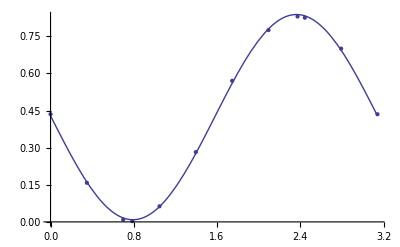

```mathematica
bkgrd=0;
angles= Join[Table[i,{i,0,180,20}],{136,45}]π/180;
powers={0.435,0.158,0.00925,0.063,0.282,0.57,0.775,0.825,0.7,0.435,0.83,0.0031}-bkgrd;
data=Thread[{angles,powers}];
fitfn=A Cos[ 2(θ+θ0)] + Offs;
fit=FindFit[data,fitfn, {θ0,{A,5},{Offs,5}},θ];
Show[
{ListPlot[data],
Plot[fitfn/.fit,{θ,0,π}]
}
]
```